```mathematica
SetDirectory["/home/jadeleon/Documents/component-erasing-maps"];
Import["mathematica/quantumJA.m"];
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Spanish";
TwoQubits=ToExpression[Import["results/TwoQubits.txt","List"]];
OneQubit=ToExpression[Import["results/OneQubit.txt","List"]];
```

```mathematica
(PCE[#,1]//Eigensystem)&/@OneQubit
```

{{{1/2,0,0,0},{{1,0,0,1},{-1,0,0,1},{0,0,1,0},{0,1,0,0}}},{{1/2,1/2,0,0},{{1,0,0,1},{0,1,1,0},{-1,0,0,1},{0,-1,1,0}}},{{1/2,1/2,0,0},{{1,0,0,1},{0,-1,1,0},{-1,0,0,1},{0,1,1,0}}},{{1/2,1/2,0,0},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}},{{1/2,1/2,1/2,1/2},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}}

```mathematica
(PCE[#,1]//Eigensystem)&/@{{1,1,1,0},{1,1,0,1},{1,0,1,1}}
```

{{{1/2,1/2,1/2,0},{{1,0,0,1},{0,0,1,0},{0,1,0,0},{-1,0,0,1}}},{{1/2,1/2,1/2,0},{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,-1,1,0}}},{{1/2,1/2,1/2,0},{{0,0,0,1},{0,-1,1,0},{1,0,0,0},{0,1,1,0}}}}

00+11, 01,10,-00+11

11, 01+10,00,-01+10

11, -01+10,00,01+10

```mathematica
(PCE[#,1]//Reshuffle//Eigensystem)&/@OneQubit
```

{{{1/4,1/4,1/4,1/4},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}},{{1/2,1/2,0,0},{{1,0,0,1},{0,1,1,0},{-1,0,0,1},{0,-1,1,0}}},{{1/2,1/2,0,0},{{1,0,0,1},{0,-1,1,0},{-1,0,0,1},{0,1,1,0}}},{{1/2,1/2,0,0},{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,0}}},{{1,0,0,0},{{1,0,0,1},{-1,0,0,1},{0,0,1,0},{0,1,0,0}}}}

```mathematica
(PCE[#,1]//Reshuffle//Eigensystem)&/@{{1,1,1,0},{1,1,0,1},{1,0,1,1}}
```

{{{3/4,-1/4,1/4,1/4},{{1,0,0,1},{-1,0,0,1},{0,0,1,0},{0,1,0,0}}},{{3/4,-1/4,1/4,1/4},{{1,0,0,1},{0,-1,1,0},{-1,0,0,1},{0,1,1,0}}},{{3/4,-1/4,1/4,1/4},{{1,0,0,1},{0,1,1,0},{-1,0,0,1},{0,-1,1,0}}}}

## Las matrices de Choi de canales (buenos)

1/4,1/4,1/4,1/4:11,10,01,00

1/2,1/2,0,0:00+11, 01+10,-00+11,-01+10

1/2,1/2,0,0:00+11, -01+10,-00+11,01+10

1/2,1/2,0,0:11, 00,10,01

1,0,0,0:00+11, -00+11,10,01

## Las matrices de Choi de NO canales (malos)

3/4,-1/4,1/4,1/4:00+11, -00+11,10,01

3/4,-1/4,1/4,1/4:00+11, -01+10,-00+11,01+10

3/4,-1/4,1/4,1/4:00+11, 01+10,-00+11,-01+10

Entrada: lista con un vector
Salida: el vector escrito en notación de Dirac

```mathematica
BaseForm[2,2]
```

10_2

```mathematica
IntegerString[#,2]&/@((Position[{1,0,0,1,1,0,1,1},1]//Flatten)-1)
```

{0,11,100,110,111}

```mathematica
Print[#]&/@{"0","11","100","110","111"};
```

0

11

100

110

111

```mathematica
IntegerString[7,2]
```

111

```mathematica
StringJoin["0","111"]/@{"0","11","100","110","111"}
```

0111

```mathematica
StringLength[#]&/@{"0","11","100","110","111"}
```

{1,2,3,3,3}

```mathematica
PCE[TwoQubits[[3]],2]//Reshuffle//Eigensystem
```

{{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,0,0,0,0,0,0,0,0},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
a=IntegerString[#,2,4]&/@((Position[{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},1]//Flatten)-1);
#&/@a//Total
```

1010+1111

```mathematica
Delete[Range[16],Position[{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},0]]
```

{11,16}

```mathematica
vec={0,-1,1,0};
```

```mathematica
a=IntegerString[#,2,4]&/@{11,16};
vec[[#]]IntegerString[#,2,4]&/@a//Total
```

Part::pspec1: Part specification 1011 is not applicable.

Part::pspec1: Part specification 0000 is not applicable.

0000 {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1}⟦0000⟧+1011 {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1}⟦1011⟧

```mathematica
b={{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
(a=Delete[Range[Length[#]],Position[#,0]];
vec=#;
(vec[[#]]IntegerString[#-1,2,4])&/@a//Total)&/@b
```

{1010+1111,-1011+1110,1000+1101,-1001+1100,0010+0111,-0011+0110,0000+0101,-0001+0100,-1010+1111,1011+1110,-1000+1101,1001+1100,-0010+0111,0011+0110,-0000+0101,0001+0100}

```mathematica
Dirac[{1,0,1,2}]
```

00+10+2 11

```mathematica
Dirac[#]&/@(PCE[TwoQubits[[3]],2]//Reshuffle//Eigenvectors)
```

{1010+1111,-1011+1110,1000+1101,-1001+1100,0010+0111,-0011+0110,0000+0101,-0001+0100,-1010+1111,1011+1110,-1000+1101,1001+1100,-0010+0111,0011+0110,-0000+0101,0001+0100}

```mathematica
Dirac[#]&/@(PCE[TwoQubits[[27]],2]//Reshuffle//Eigenvectors)
```

{1111,1010,0101,0000,1110,1101,1100,1011,1001,1000,0111,0110,0100,0011,0010,0001}

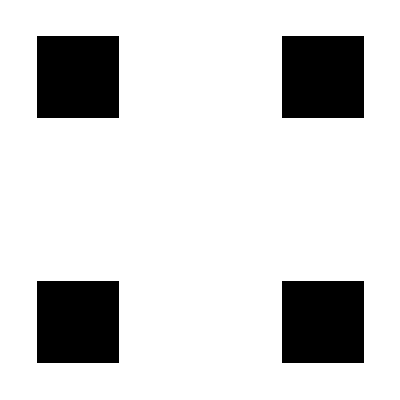

```mathematica
TwoQBoard[TwoQubits[[27]]]
```

#### Ahora necesito implementar una rutina para sacar sólo los estados asociados a los eigenvalores malos

```mathematica
Dirac[#]&/@(PCE[#]//Reshuffle//Eigenvectors)
```

{1111,1100,1010,1001,0110,0101,0011,0000,1110,1101,1011,1000,0111,0100,0010,0001}

```mathematica
((PCE[#]//Reshuffle//Eigenvectors)&/@TwoQubits[[19;;19+8]])[[;;,1;;4]];
Map[Dirac,%,{2}]
```

{{0000+0101+1010+1111,0001+0100+1011+1110,0010+0111+1000+1101,0011+0110+1001+1100},{0000+0101+1010+1111,-0001+0100-1011+1110,0010+0111+1000+1101,-0011+0110-1001+1100},{0101+1111,0111+1101,0000+1010,0010+1000},{0000+0101+1010+1111,0001+0100+1011+1110,-0010-0111+1000+1101,-0011-0110+1001+1100},{0000+0101+1010+1111,-0001+0100-1011+1110,-0010-0111+1000+1101,0011-0110-1001+1100},{0101+1111,-0111+1101,0000+1010,-0010+1000},{1010+1111,1011+1110,0000+0101,0001+0100},{1010+1111,-1011+1110,0000+0101,-0001+0100},{1111,1010,0101,0000}}

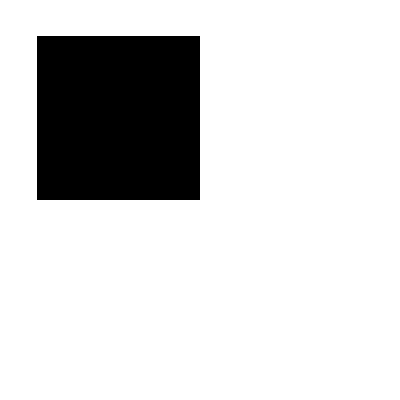
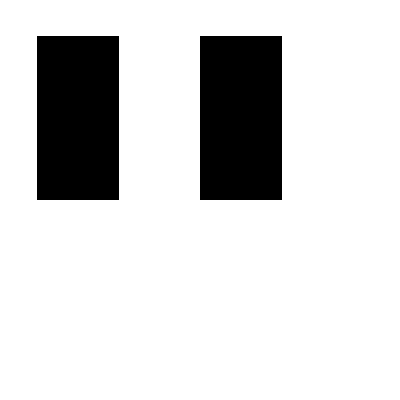
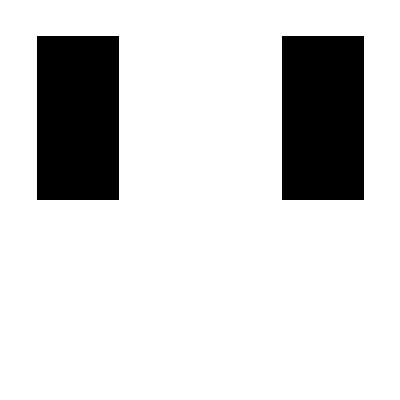
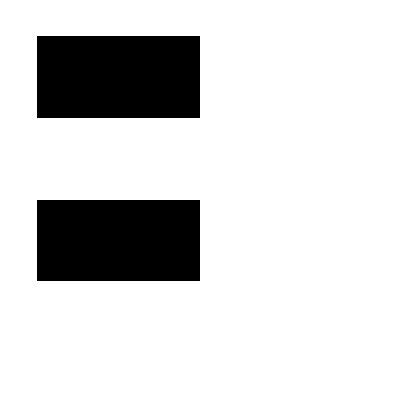
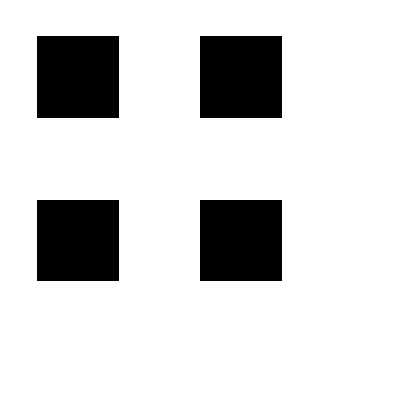
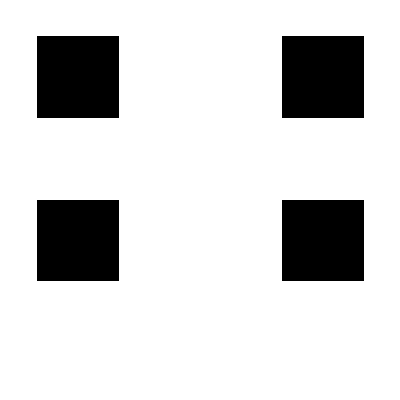
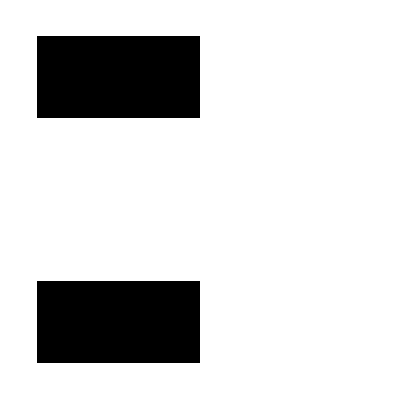
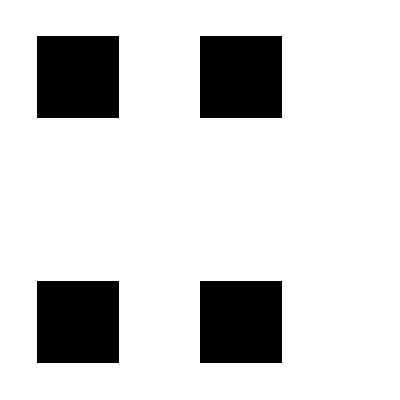
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TwoQBoard[#]&/@TwoQubits[[19;;19+8]]
```

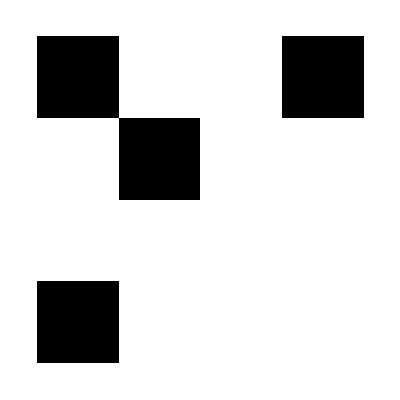

{1,1,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2,0,0,0,0,0,0}

{-0011+1100,-0110+1001}

```mathematica
try=SparseArray[{{1,1},{1,4},{4,1},{2,2}}->{1,1,1,1},{4,4}]//Normal;
ArrayPlot[try]
PCE[try//Flatten,2]//Reshuffle//Eigenvalues
Dirac[#]&/@(PCE[try//Flatten,2]//Reshuffle//Eigenvectors)[[3;;4]]
```

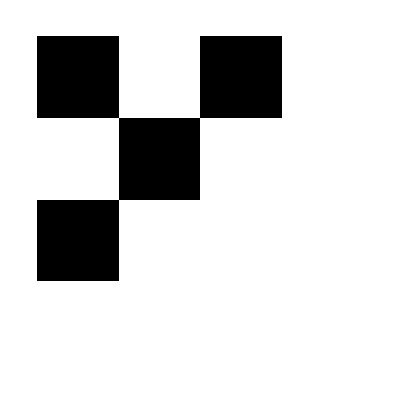

{1,1,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2,0,0,0,0,0,0}

{-0001-0100+1011+1110,-0010+0111-1000+1101}

```mathematica
try=SparseArray[{{1,1},{1,3},{3,1},{2,2}}->{1,1,1,1},{4,4}]//Normal;
ArrayPlot[try]
PCE[try//Flatten,2]//Reshuffle//Eigenvalues
Dirac[#]&/@(PCE[try//Flatten,2]//Reshuffle//Eigenvectors)[[3;;4]]
```

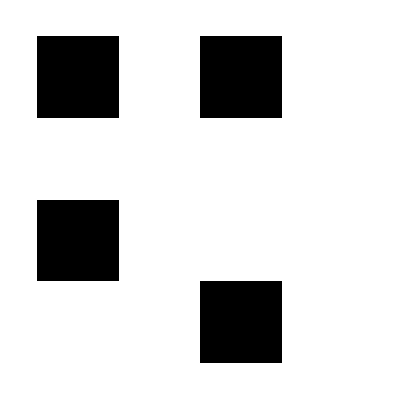

{1,1,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,1/2,0,0,0,0,0,0}

{0000-0101-1010+1111,-0001-0100+1011+1110}

```mathematica
try=SparseArray[{{1,1},{1,3},{3,1},{4,3}}->{1,1,1,1},{4,4}]//Normal;
ArrayPlot[try]
PCE[try//Flatten,2]//Reshuffle//Eigenvalues
Dirac[#]&/@(PCE[try//Flatten,2]//Reshuffle//Eigenvectors)[[3;;4]]
```

0110+1100=(0_1 1_3)